## 3.029 Spring 2022 Lecture 08 - 02/23/2022

## Physical Properties of Crystals

Physical properties or observables are measurable quantities of the state of a physical system.

While certain physical properties, like the mass density of a material, are isotropic, preferred directions in crystals imply that others, such as the stiffness tensor of elastic materials, depend on direction.

Since physical properties represent measurable quantities, they are by definition measured in a particular reference frame.

It stands to reason, that if a set of measurements in a different reference frame represent the same physical property, there must exist  transformation between the two reference frames relating the measured physical quantities.

In this section, we will introduce this relationship.

## Coordinate Transformations (Review)

We can define a transformation between two sets of reference frames

and

where the matrix α_ijrepresents the direction cosines between the two reference frames

-Graphics-

In-fact, you’ve seen this before in the notebook `3.019_L12=Change_of_Basis_Stiffness_Outline.nb` from last semester (which I’ve uploaded again on canvas)!

We will quickly review some concepts here, and extend the analysis to Thermodynamic stability

### Einstein Summation Convention

Left-Multiplying a vector with a matrix

Multiplication of Matrices

where

### Rotating a Rank - 2 Tensor

Consider an “old” (Orange) and a “new” (Blue) coordinate system

Denote the direction cosines matrix mapping a vector from one coordinate system to another as

-Graphics-

-Graphics-

is the same vector, but expressed in a different coordinate systems.

For example, suppose the "Blue coordinate system" is rotated by Pi/4 around the z-axis from the Orange (original) one.

```mathematica
orangeVector = {1,3,-1};
blueVector = RotationMatrix[Pi/4,{0,0,1}].orangeVector
```

{-√2,2 √2,-1}

```mathematica
Inverse[RotationMatrix[Pi/4,{0,0,1}]].blueVector
```

{1,3,-1}

Physical property tensors in either coordinate system are given by:

-Graphics-
-Graphics-

These are the same vectors and same rank-2 tensors, but expressed in different coordinate systems.

Suppose now we know a rank-2 physical property tensor in the old (orange) coordinate system
-Graphics-

How do we express the same physical property tensor, but in the blue coordinate system?

Transform the vectors
-Graphics-

Left-multiply by the inverse  
-Graphics-

Note that the inverse of going from blue to orange is going from orange to blue we have:
-Graphics-

This finally gives the relations:
-Graphics-
and
-Graphics-

Example: Rotation of π/2 around [0,0,1]

Rank-2 tensor in “old” coordinate system

```mathematica
MatrixForm[orangeRank2Tensor= Table[Indexed[m,Sort[{i,j}]],{i,3},{j,3}]]
```

(m11 | m12 | m13
m12 | m22 | m23
m13 | m23 | m33)

Transformation from “orange” to “blue”

```mathematica
MatrixForm[orangeToBlue = RotationMatrix[Pi/2,{0,0,1}]]
```

(0 | -1 | 0
1 | 0 | 0
0 | 0 | 1)

The inverse transformation from “blue” to “orange”

```mathematica
MatrixForm[blueToOrange=Simplify[ Inverse[orangeToBlue]]]
```

(0 | 1 | 0
-1 | 0 | 0
0 | 0 | 1)

Note: For symmetry operators such as rotations (which have determinant = 1), the inverse is the same as the transpose.

The Rank-2 tensor in the “new” coordinate system is given by:

```mathematica
MatrixForm[Simplify[orangeToBlue.orangeRank2Tensor.blueToOrange]]
```

(m22 | -m12 | -m23
-m12 | m11 | m13
-m23 | m13 | m33)

## Intrinsic “Tensor” Symmetries

### Paramagnetism / Diamagnetism

Consider a magnetized crystal 

-Graphics-

The work done by the battery is given by:

The first term is related to Joule heating and does not depend on the magnetic field, H_i or magnetic induction, B_i direction

The second term updates our fundamental thermodynamic relation to read:

We can relate the magnetic induction, B, and magnetic field, H, using a constitutive relationship given by

where I is the magnetization intensity

In isotropic materials, we can express the intensity of magnetization to the field strength using

where ψ is the magnetic susceptibility

More generally, the intensity of magnetization need to be parallel to the applied field, giving for anisotropic crystals

Combining these, we obtain the additional work term as

where we’ve introduced the permeability tensor μ_ij=μ_0(δ_ij+ψ_ij)

If we write this out fully we have:

As such we can write:

Differentiating the first expression wrt H_2 and the second wrt H_1 we obtain

However, we know from the equality of mixed partials that these should be identical

Thus we conclude that μ_ij=μ_ji

This is an “intrinsic” tensor symmetry, which states that the permeability tensor is invariant under permutation of the indices i ↔ j

I.e. the rank-2 tensor is symmetric.

### Independent Components

Since the only condition we have so-far on our rank-2 tensor is that it be symmetric

We are free to choose its remaining d(d-+1)/2 components

These are called the independent tensor components, and the most general rank-2 tensor is given in terms of its symbolic independent components

```mathematica
MatrixForm[Table[Indexed[μ,Sort[{i,j}]],{i,3},{j,3}]]
```

(μ11 | μ12 | μ13
μ12 | μ22 | μ23
μ13 | μ23 | μ33)

Note: We used Indexed to offer a symbolic indexing scheme

```mathematica
Indexed[μ,{1,2}]
```

μ12

In this case, it’s rather easy to specify the condition for symmetry

Namely, we sort the indices in ascending order (i.e. keep μ_12 over μ_21)

However, for higher-rank tensors with more complicated symmetries - we might not always be able to intuit the conditions

Fortunately, there's a very convenient way to express these in the Wolfram Language

```mathematica
MatrixForm[
permeabilityTensor=
With[{symbolName=μ,d=3},
Normal[
SymmetrizedArray[pos_:>Indexed[symbolName,pos],{d,d},{
{Cycles[{{1,2}}],1}}
]]]]
```

(μ11 | μ12 | μ13
μ12 | μ22 | μ23
μ13 | μ23 | μ33)

This looks complicated - but it generalizes very nicely!

Let's break it down. SymmetrizedArray takes three arguments:

A list of rules of how to specify each component
here we’re just using a symbolic indexing scheme like above

The dimensions the array is valid in
here we specified 3D

A list of symmetries, e.g. using “Generators”
here we specify that upon permutation of the 1st and 2nd indices, the tensor gets multiplied by 1 (i.e. is the same)

Note: If instead our tensor was anti-symmetric, we would have specified a -1 instead

### Stiffness and Compliance

In 3.013 last semester, you talked about elastic properties of solids which connect the stress state of a material with its strain

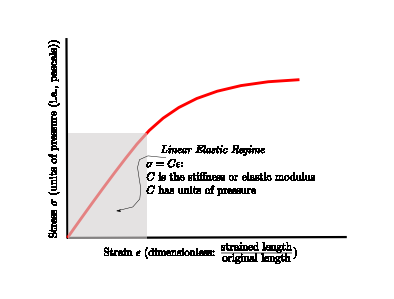
I suspect you probably had a tensile testing lab which had you plot figures like this?

-Graphics-

In the linear elastic regime, the stress increases linearly with increasing strain.

When the stress (or strain) is large enough, the material softens (becomes less stiff).

A good mental picture is a Hooke's law spring's force versus displacement curve.

We will investigate the nature of stresses and strains.

An important take-away is that stresses and strains are not so simple as the plot above

they are not scalars that can be represented by a single axis

Instead, stresses and strains are rank-2 tensors

#### Stress Tensor

The units of stress are Newtons/Meters^2

It is instructive to think of stress as representing the ratio between two vector quantities

The force vector

and the area vector

Since these two vectors can be independently varied, the stress tensor is rank-2 tensor w/ two indices

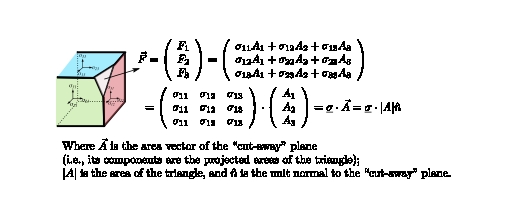

Moreover, for the material to be in static-equilibrium we require that the stress tensor be symmetric

We won’t prove this but Nye’s Physical Properties of Crystals is an excellent resource (for all things physical properties)

#### Strain Tensor

Similarly, the strain tensor combines information from two local vectors.

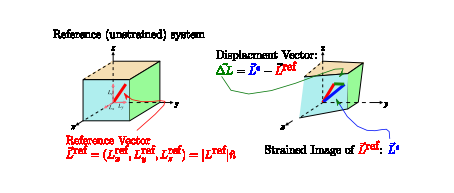
Consider two line segments in a small region near a given point.
1) (L⃗)^ref which is a reference vector in the original unstrained body. You can think of it as a line segment.
2) (L⃗)^ϵ which is the image reference vector in the strained body.

-Graphics-

The deformation gradient tensor is therefore given by

The symmetrical part of this rank-two tensor is the strain-tensor

Note: the antisymmetrical part describes rigid-body rotation which we assume does not generate any stress

#### Generalized Hooke’s Law

Armed with our definitions for stress and strain as rank-2 tensors

we can write a generalization of Hooke’s law using index notation

where we’ve introduced the rank-4 compliance tensor

Note: we are still in the linear-elastic regime

In general a rank-4 tensor in 3D has 3^4=81 components

```mathematica
MatrixForm[
generalRank4Tensor=
With[{symbolName=s,d=3},
Normal[
SymmetrizedArray[pos_:>Indexed[symbolName,pos],{d,d,d,d},{}]]]]
```

((s1111 | s1112 | s1113
s1121 | s1122 | s1123
s1131 | s1132 | s1133) | (s1211 | s1212 | s1213
s1221 | s1222 | s1223
s1231 | s1232 | s1233) | (s1311 | s1312 | s1313
s1321 | s1322 | s1323
s1331 | s1332 | s1333)
(s2111 | s2112 | s2113
s2121 | s2122 | s2123
s2131 | s2132 | s2133) | (s2211 | s2212 | s2213
s2221 | s2222 | s2223
s2231 | s2232 | s2233) | (s2311 | s2312 | s2313
s2321 | s2322 | s2323
s2331 | s2332 | s2333)
(s3111 | s3112 | s3113
s3121 | s3122 | s3123
s3131 | s3132 | s3133) | (s3211 | s3212 | s3213
s3221 | s3222 | s3223
s3231 | s3232 | s3233) | (s3311 | s3312 | s3313
s3321 | s3322 | s3323
s3331 | s3332 | s3333))

```mathematica
Variables[generalRank4Tensor]//Length
```

81

However, since both the stress and strain tensor are symmetric tensors (i.e. σ_ij=σ_ji & ϵ_ij=ϵ_ji)

We conclude that the compliance tensor also has these symmetries (i.e. s_ijkl=s_jikl=s_ijlk)

This reduces the independent components to 36

```mathematica
MatrixForm[
minorSymmetriesRank4Tensor=
With[{symbolName=s,d=3},
Normal[
SymmetrizedArray[pos_:>Indexed[symbolName,pos],{d,d,d,d},{
{Cycles[{{1,2}}],1},
{Cycles[{{3,4}}],1}
}]]]]
```

((s1111 | s1112 | s1113
s1112 | s1122 | s1123
s1113 | s1123 | s1133) | (s1211 | s1212 | s1213
s1212 | s1222 | s1223
s1213 | s1223 | s1233) | (s1311 | s1312 | s1313
s1312 | s1322 | s1323
s1313 | s1323 | s1333)
(s1211 | s1212 | s1213
s1212 | s1222 | s1223
s1213 | s1223 | s1233) | (s2211 | s2212 | s2213
s2212 | s2222 | s2223
s2213 | s2223 | s2233) | (s2311 | s2312 | s2313
s2312 | s2322 | s2323
s2313 | s2323 | s2333)
(s1311 | s1312 | s1313
s1312 | s1322 | s1323
s1313 | s1323 | s1333) | (s2311 | s2312 | s2313
s2312 | s2322 | s2323
s2313 | s2323 | s2333) | (s3311 | s3312 | s3313
s3312 | s3322 | s3323
s3313 | s3323 | s3333))

```mathematica
Variables[minorSymmetriesRank4Tensor]//Length
```

36

An equivalent definition to the compliance would be to introduce the stiffness tensor

which has the same “intrinsic” tensor-symmetries as the compliance tensor

Note: Yes, it’s curious that stiffness uses the symbol, c, and compliance used the symbol, s

#### Strain Energy

A strained crystal does work, in-fact we’ve already seen this work term multiple times

Consider a hydrostatic stress state (i.e. one with σ_11=σ_22=σ_33=-P)

Since all the off-diagonal terms are zero, we the only relevant strains are dϵ_11, dϵ_22, and dϵ_33

remembering the definition of strain: ϵ_11=Δl_1/l_1, and substituting l_1 l_2 l_3=V, we can generalize

as the strain energy:

As such, in a reversible (isoentropic) process, we can substitute our generalized Hookes law to obtain:

Similarly, with the Diamagnetism case above - since Ψ is a total differential, we can take its derivative it in any order

and thus we conclude that the stiffness tensor additionally has (ij) ↔ (kl) symmetry
Note: we’re permuting the indices as a pair

A similar argument ensures the compliance tensor has s_ijkl=s_klij symmetry

```mathematica
MatrixForm[
complianceTensorSymbolic=
With[{symbolName=s,d=3},
Normal[
SymmetrizedArray[pos_:>Indexed[symbolName,pos],{d,d,d,d},{
{Cycles[{{1,2}}],1},
{Cycles[{{3,4}}],1},
{Cycles[{{1,3},{2,4}}],1}
}]]]]
```

((s1111 | s1112 | s1113
s1112 | s1122 | s1123
s1113 | s1123 | s1133) | (s1112 | s1212 | s1213
s1212 | s1222 | s1223
s1213 | s1223 | s1233) | (s1113 | s1213 | s1313
s1213 | s1322 | s1323
s1313 | s1323 | s1333)
(s1112 | s1212 | s1213
s1212 | s1222 | s1223
s1213 | s1223 | s1233) | (s1122 | s1222 | s1322
s1222 | s2222 | s2223
s1322 | s2223 | s2233) | (s1123 | s1223 | s1323
s1223 | s2223 | s2323
s1323 | s2323 | s2333)
(s1113 | s1213 | s1313
s1213 | s1322 | s1323
s1313 | s1323 | s1333) | (s1123 | s1223 | s1323
s1223 | s2223 | s2323
s1323 | s2323 | s2333) | (s1133 | s1233 | s1333
s1233 | s2233 | s2333
s1333 | s2333 | s3333))

This reduces the independent components further to 21!

```mathematica
Length[Variables[complianceTensorSymbolic]]
```

21

## Neumann’s Principle

So far, we’ve seen how physical properties are tensors which transform under coordinate transformations

And we’ve derived the most general symbolic tensors for some common material properties

You will get more practice in assignment 2!

The next step is to see how crystal symmetry constrains these independent components further

This is summarized nicely by Neumann's principle, which states that:

"The symmetry elements of any physical property of a crystal must include the symmetry elements of the point group of that crystal"

What this means for us, is that if we rotate a tensor using any of the symmetry operations of its point group, the resulting tensor must be identical to the one with started with

This therefore enforces “crystal symmetry” constraints of the form of the tensor

As an example, let’s suppose we are looking at a material which has a four-fold rotation symmetry along the z-axis

```mathematica
MatrixForm[fourFoldRotation=RotationMatrix[π/4,{0,0,1}]]
```

(1/(√2) | -1/(√2) | 0
1/(√2) | 1/(√2) | 0
0 | 0 | 1)

And rotate the rank-2 permeability tensor we derived above using our coordinate transformation

Note:  I used the transpose instead of the inverse, since the determinant of our rotation transformation is 1

```mathematica
MatrixForm[rotatedPermeabilityTensor=Simplify[fourFoldRotation.permeabilityTensor.Transpose[fourFoldRotation]]
]
```

(1/2 (μ11-2 μ12+μ22) | 1/2 (μ11-μ22) | (μ13-μ23)/(√2)
1/2 (μ11-μ22) | 1/2 (μ11+2 μ12+μ22) | (μ13+μ23)/(√2)
(μ13-μ23)/(√2) | (μ13+μ23)/(√2) | μ33)

Neumann’s principle tells us that these two tensors must be identical

```mathematica
neumannConditions=Thread[Flatten[permeabilityTensor]==Flatten[rotatedPermeabilityTensor]]
```

{μ11==1/2 (μ11-2 μ12+μ22),μ12==1/2 (μ11-μ22),μ13==(μ13-μ23)/(√2),μ12==1/2 (μ11-μ22),μ22==1/2 (μ11+2 μ12+μ22),μ23==(μ13+μ23)/(√2),μ13==(μ13-μ23)/(√2),μ23==(μ13+μ23)/(√2),True}

Which enforces the following constraints

```mathematica
neumannConstraints=First[Solve[neumannConditions,Variables[permeabilityTensor]]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{μ12→0,μ13→0,μ22→μ11,μ23→0}

As such, the most general permeability tensor for a material with a four-fold rotation axis around the z-axis (e.g.Tetragonal systems) takes the form

```mathematica
MatrixForm[permeabilityTensor/.neumannConstraints]
```

(μ11 | 0 | 0
0 | μ11 | 0
0 | 0 | μ33)

More generally, Neumann’s principle can be expressed for arbitrary-rank tensors as

where R_ij is any point group operation of the crystal

E.g. for rank-2 tensors we have

and similarly for rank-4 tensors

You will explore this form further in your second assignment!

## Stability Constraints

### Poisson’s Ratio

In addition to the “intrinsic” tensor symmetries and the crystal symmetries introduced by the material’s point group, which determine the independent components in tensors, thermodynamic stability places additional constraints on the values those components can take

As an example, we’ll look at the compliance tensor for an isotropic material

As we saw above, the compliance tensor, s_ijkl, is a rank-4 tensor given by the defining equation:

Since the tensor has both  and  symmetry, we can use a condensed matrix notation instead

where the indices now run from 1-6, with the following scheme:

1 → 11

2 → 22

3 → 33

4 → 23, 32

5 → 13, 31

6 → 12, 21

For an isotropic material, crystal symmetry reduces to matrix to

```mathematica
MatrixForm[isotropicComplianceMatrix={{s11,s12,s12,0,0,0},{s12,s11,s12,0,0,0},{s12,s12,s11,0,0,0},{0,0,0,2 (s11-s12),0,0},{0,0,0,0,2 (s11-s12),0},{0,0,0,0,0,2 (s11-s12)}}]
```

(s11 | s12 | s12 | 0 | 0 | 0
s12 | s11 | s12 | 0 | 0 | 0
s12 | s12 | s11 | 0 | 0 | 0
0 | 0 | 0 | 2 (s11-s12) | 0 | 0
0 | 0 | 0 | 0 | 2 (s11-s12) | 0
0 | 0 | 0 | 0 | 0 | 2 (s11-s12))

Introducing the more common  notation

where E is Young's Modulus, G is the Rigidity (or Shear) Modulus, and  is Poisson's ratio, we obtain

```mathematica
MatrixForm[
isotropicComplianceMatrix = Simplify[isotropicComplianceMatrix/.{Indexed[s,{1,1}]-> 1/Ε,Indexed[s,{1,2}]-> -ν/Ε}]]
```

(1/Ε | -ν/Ε | -ν/Ε | 0 | 0 | 0
-ν/Ε | 1/Ε | -ν/Ε | 0 | 0 | 0
-ν/Ε | -ν/Ε | 1/Ε | 0 | 0 | 0
0 | 0 | 0 | (2 (1+ν))/Ε | 0 | 0
0 | 0 | 0 | 0 | (2 (1+ν))/Ε | 0
0 | 0 | 0 | 0 | 0 | (2 (1+ν))/Ε)

As we saw above, the strain energy stored in a crystal is given by

Which must be positive for thermodynamic stability, suggesting  must be positive semi-definite

```mathematica
Reduce[Thread[Eigenvalues[isotropicComplianceMatrix] >= 0],{Ε,ν},Reals]
```

Ε>0&&-1≤ν≤1/2

Which specifies that Young’s Modulus must be positive, and that Poisson’s ratio can only take values between -1 and 1/2

In-fact, a material with a Poisson ratio of 1/2 is incompressible

### Zener Ratio

For cubic materials instead, the compliance tensor is given by

```mathematica
MatrixForm[
cubicComplianceMatrix={{s11,s12,s12,0,0,0},{s12,s11,s12,0,0,0},{s12,s12,s11,0,0,0},{0,0,0,s44,0,0},{0,0,0,0,s44,0},{0,0,0,0,0,s44}}]
```

(s11 | s12 | s12 | 0 | 0 | 0
s12 | s11 | s12 | 0 | 0 | 0
s12 | s12 | s11 | 0 | 0 | 0
0 | 0 | 0 | s44 | 0 | 0
0 | 0 | 0 | 0 | s44 | 0
0 | 0 | 0 | 0 | 0 | s44)

Where the extra independent component is related to  and  with the Zener ratio:

```mathematica
MatrixForm[
cubicComplianceMatrix=cubicComplianceMatrix/.s44->2(s11-s12)/α]
```

(s11 | s12 | s12 | 0 | 0 | 0
s12 | s11 | s12 | 0 | 0 | 0
s12 | s12 | s11 | 0 | 0 | 0
0 | 0 | 0 | (2 (s11-s12))/α | 0 | 0
0 | 0 | 0 | 0 | (2 (s11-s12))/α | 0
0 | 0 | 0 | 0 | 0 | (2 (s11-s12))/α)

```mathematica
Reduce[Thread[Eigenvalues[cubicComplianceMatrix] > 0],{s11,s12,α},Reals]
```

s11>0&&-s11/2<s12<s11&&α>0

Which must be a positive constant according to thermodynamic stability